## MAE 280 B - Linear Control Design Mauricio de Oliveira State Estimation

```mathematica
Hyperlink["http://fccr.ucsd.edu/~mauricio/courses/mae280b"]
```

## Problem Data

```mathematica
m = 100. (* 100 kg *);
r = 300. 10^3 (* 300 km *);
R0 = 6.37 10^6 (* 6.37 10^3 km *);
G = 6.673 10^-11 (* 6.673 N m^2/kg^2 *);
M = 5.98 10^24 (* 5.98 10^24 kg *);
```

Gravitational force constant

```mathematica
k = G M;
```

Angular velocity (rad/s)

```mathematica
ω = Sqrt[k/((R0+r)^3)]
```

0.00115964

“Ground” velocity (m/s)

```mathematica
v = ω*(R0+r)
```

7734.78

Noise variances

```mathematica
Ww = 0.1 IdentityMatrix[2];
```

### Linearized System Realization (radial and tangential position measurement)

```mathematica
A = {
{0,0,1,0},
{0,0,0,1},
{3 ω^2,0,0,2(r+R0)ω},
{0,0,(-2ω)/(r+R0),0}
};
Bw=Bu = {
{0,0},
{0,0},
{1/m,0},
{0,1/(m(r+R0))}
};
Cy={
{0,r+R0,0,0},
{1,0,0,0}
};
```

### Scaling

```mathematica
linearizedSystem=StateSpaceModel[{A,Bw,Cy}]
```

(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
4.03428×10^-6 | 0 | 0 | 15469.6 | 0.01 | 0
0 | 0 | -3.47718×10^-10 | 0 | 0 | 1.49925×10^-9
0 | 6.67×10^6 | 0 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0 | 0)_^𝒮

```mathematica
T = DiagonalMatrix[{1,r+R0,1,r+R0}]
```

{{1.,0.,0.,0.},{0.,6.67×10^6,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,6.67×10^6}}

Apply the similarity transformation

```mathematica
transformedLinearizedSystem=StateSpaceTransform[linearizedSystem,Inverse[T]]
```

(0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.
4.03428×10^-6 | 0. | 0. | 0.00231928 | 0.01 | 0.
0. | 0. | -0.00231928 | 0. | 0. | 0.01
0. | 1. | 0. | 0. | 0 | 0
1. | 0. | 0. | 0. | 0 | 0)_^𝒮

```mathematica
Bwt = T.Bw;
```

## Filter design using dual state feedback

```mathematica
dualSystem = StateSpaceModel[{Transpose[A],Transpose[Cy],Transpose[Bw]}]
```

(0 | 0 | 4.03428×10^-6 | 0 | 0 | 1
0 | 0 | 0 | 0 | 6.67×10^6 | 0
1 | 0 | 0 | -3.47718×10^-10 | 0 | 0
0 | 1 | 15469.6 | 0 | 0 | 0
0 | 0 | 0.01 | 0 | 0 | 0
0 | 0 | 0 | 1.49925×10^-9 | 0 | 0)_^𝒮

```mathematica
transformedDualSystem=StateSpaceTransform[dualSystem,Transpose[T]]
```

(0. | 0. | 4.03428×10^-6 | 0. | 0. | 1.
0. | 0. | 0. | 0. | 1. | 0.
1. | 0. | 0. | -0.00231928 | 0. | 0.
0. | 1. | 0.00231928 | 0. | 0. | 0.
0. | 0. | 0.01 | 0. | 0 | 0
0. | 0. | 0. | 0.01 | 0 | 0)_^𝒮

```mathematica
Wv = 0.1IdentityMatrix[2];
```

```mathematica
Ft=-Transpose[LQRegulatorGains[transformedDualSystem,{Bwt.Ww.Transpose[Bwt],Wv}]];
MatrixForm[Ft]
```

(2.33931×10^-7 | -0.14144
-0.141412 | 2.33931×10^-7
-0.00016397 | -0.0100027
-0.00999866 | 0.000164036)

## Filter design using Kalman

```mathematica
filter= KalmanEstimator[transformedLinearizedSystem, {Ww, Wv}]
```

(-0.14144 | 2.33931×10^-7 | 1. | 0. | -2.33931×10^-7 | 0.14144
2.33931×10^-7 | -0.141412 | 0. | 1. | 0.141412 | -2.33931×10^-7
-0.00999866 | -0.00016397 | 0. | 0.00231928 | 0.00016397 | 0.0100027
0.000164036 | -0.00999866 | -0.00231928 | 0. | 0.00999866 | -0.000164036
1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
1. | 0. | 0. | 0. | 0. | 0.)_^𝒮

```mathematica
Ft = -Normal[filter][[2]];
MatrixForm[Ft]
```

(2.33931×10^-7 | -0.14144
-0.141412 | 2.33931×10^-7
-0.00016397 | -0.0100027
-0.00999866 | 0.000164036)

## Analysis of the filter

Filter gain in original coordinates :

```mathematica
F=Inverse[Transpose[T]].Ft;
MatrixForm[F]
```

(2.33931×10^-7 | -0.14144
-2.12012×10^-8 | 3.50721×10^-14
-0.00016397 | -0.0100027
-1.49905×10^-9 | 2.45931×10^-11)

Error Dynamics

```mathematica
Eigenvalues[A+ F.Cy]
```

{-0.070713+0.0718679 ⅈ,-0.070713-0.0718679 ⅈ,-0.0707131+0.0695487 ⅈ,-0.0707131-0.0695487 ⅈ}

### Augment system with measurement noise input

```mathematica
Bwa=ArrayFlatten[{{Bw,ConstantArray[0,{4,2}]}}];
Dywa=ArrayFlatten[{{ConstantArray[0,{2,2}],IdentityMatrix[2]}}];
```

```mathematica
augmentedSystem=StateSpaceModel[{A,Bwa,Cy,Dywa}]
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
4.03428×10^-6 | 0 | 0 | 15469.6 | 0.01 | 0 | 0 | 0
0 | 0 | -3.47718×10^-10 | 0 | 0 | 1.49925×10^-9 | 0 | 0
0 | 6.67×10^6 | 0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0 | 0 | 1)_^𝒮

```mathematica
transformedAugmentedSystem=StateSpaceTransform[augmentedSystem,Inverse[T]]
```

(0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
4.03428×10^-6 | 0. | 0. | 0.00231928 | 0.01 | 0. | 0. | 0.
0. | 0. | -0.00231928 | 0. | 0. | 0.01 | 0. | 0.
0. | 1. | 0. | 0. | 0 | 0 | 1 | 0
1. | 0. | 0. | 0. | 0 | 0 | 0 | 1)_^𝒮

```mathematica
Wt = ArrayFlatten[{{ArrayFlatten[{{Ww,ConstantArray[0,{2,2}]}}]},
{ArrayFlatten[{{ConstantArray[0,{2,2}],Wv}}]}}];
MatrixForm[Wt]
```

(0.1 | 0. | 0 | 0
0. | 0.1 | 0 | 0
0 | 0 | 0.1 | 0.
0 | 0 | 0. | 0.1)

### Connect system and filter

```mathematica
sys = SystemsModelSeriesConnect[transformedAugmentedSystem,filter]
```

(0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4.03428×10^-6 | 0. | 0. | 0.00231928 | 0. | 0. | 0. | 0. | 0.01 | 0. | 0. | 0.
0. | 0. | -0.00231928 | 0. | 0. | 0. | 0. | 0. | 0. | 0.01 | 0. | 0.
0.14144 | -2.33931×10^-7 | 0. | 0. | -0.14144 | 2.33931×10^-7 | 1. | 0. | 0. | 0. | -2.33931×10^-7 | 0.14144
-2.33931×10^-7 | 0.141412 | 0. | 0. | 2.33931×10^-7 | -0.141412 | 0. | 1. | 0. | 0. | 0.141412 | -2.33931×10^-7
0.0100027 | 0.00016397 | 0. | 0. | -0.00999866 | -0.00016397 | 0. | 0.00231928 | 0. | 0. | 0.00016397 | 0.0100027
-0.000164036 | 0.00999866 | 0. | 0. | 0.000164036 | -0.00999866 | -0.00231928 | 0. | 0. | 0. | 0.00999866 | -0.000164036
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)_^𝒮

### Simulate

```mathematica
h=.01;
```

```mathematica
Tmax = 200;
T = Table[i,{i,0,Tmax,h}];
w = MapThread[Flatten[{#1,#2}]&,{RandomVariate[NormalDistribution[],{Length[T],2}].MatrixPower[Ww,.5],RandomVariate[NormalDistribution[],{Length[T],2}].MatrixPower[Wv,.5]}];
```

Estimate stationary position

```mathematica
x0 = {0,0,0,0};
xhat0 = {-6,20,0,0};
```

```mathematica
sysDiscrete = ToDiscreteTimeModel[sys,h];
{y,t,x}= {OutputResponse[{sysDiscrete,Join[x0,xhat0]},Transpose[w]],T,StateResponse[{sysDiscrete,Join[x0,xhat0]},Transpose[w]]};
```

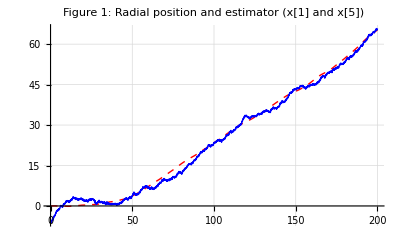

```mathematica
plots={{t,x[[1]]},{t,x[[5]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 1: Radial position and estimator (x[1] and x[5])",Joined->True,PlotStyle->{{Red,Dashed},Blue},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

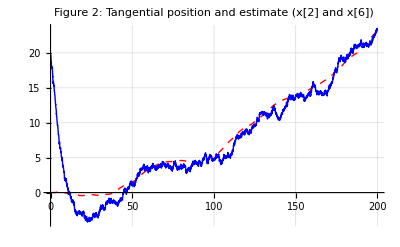

```mathematica
plots={{t,x[[2]]},{t,x[[6]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 2: Tangential position and estimate (x[2] and x[6])",Joined->True,PlotStyle->{{Red,Dashed},Blue},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

## Linearized System Realization (tangential position and radial velocity measurement)

```mathematica
A = {
{0,0,1,0},
{0,0,0,1},
{3 ω^2,0,0,2(r+R0)ω},
{0,0,(-2ω)/(r+R0),0}
};
Bw=Bu = {
{0,0},
{0,0},
{1/m,0},
{0,1/(m(r+R0))}
};
Cy={
{0,r+R0,0,0},
{0,0,1,0}
};
```

### Scaling

```mathematica
linearizedSystem=StateSpaceModel[{A,Bw,Cy}]
```

(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0
4.03428×10^-6 | 0 | 0 | 15469.6 | 0.01 | 0
0 | 0 | -3.47718×10^-10 | 0 | 0 | 1.49925×10^-9
0 | 6.67×10^6 | 0 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0)_^𝒮

```mathematica
T = DiagonalMatrix[{1,r+R0,1,r+R0}]
```

{{1.,0.,0.,0.},{0.,6.67×10^6,0.,0.},{0.,0.,1.,0.},{0.,0.,0.,6.67×10^6}}

Apply the similarity transformation

```mathematica
transformedLinearizedSystem=StateSpaceTransform[linearizedSystem,Inverse[T]]
```

(0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.
4.03428×10^-6 | 0. | 0. | 0.00231928 | 0.01 | 0.
0. | 0. | -0.00231928 | 0. | 0. | 0.01
0. | 1. | 0. | 0. | 0 | 0
0. | 0. | 1. | 0. | 0 | 0)_^𝒮

```mathematica
Bwt = T.Bw;
```

## Filter design using Kalman

```mathematica
Wv = 0.1IdentityMatrix[2];
```

```mathematica
filter= KalmanEstimator[transformedLinearizedSystem, {Ww, Wv}]
```

(0. | 0.413362 | -0.910567 | 0. | -0.413362 | 1.91057
0. | -0.141864 | 0.00181012 | 1. | 0.141864 | -0.00181012
4.03428×10^-6 | 0.00181012 | -0.0105242 | 0.00231928 | -0.00181012 | 0.0105242
0. | -0.0100644 | -0.00202176 | 0. | 0.0100644 | -0.000297516
1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0.)_^𝒮

```mathematica
Ft = -Normal[filter][[2]];
MatrixForm[Ft]
```

(0.413362 | -1.91057
-0.141864 | 0.00181012
0.00181012 | -0.0105242
-0.0100644 | 0.000297516)

## Analysis of the filter

Filter gain in original coordinates :

```mathematica
F=Inverse[Transpose[T]].Ft;
MatrixForm[F]
```

(0.413362 | -1.91057
-2.1269×10^-8 | 2.71383×10^-10
0.00181012 | -0.0105242
-1.5089×10^-9 | 4.46051×10^-11)

Error Dynamics

```mathematica
Eigenvalues[A+ F.Cy]
```

{-0.0706826+0.0707396 ⅈ,-0.0706826-0.0707396 ⅈ,-0.0106443,-0.000379004}

### Augment system with measurement noise input

```mathematica
Bwa=ArrayFlatten[{{Bw,ConstantArray[0,{4,2}]}}];
Dywa=ArrayFlatten[{{ConstantArray[0,{2,2}],IdentityMatrix[2]}}];
```

```mathematica
augmentedSystem=StateSpaceModel[{A,Bwa,Cy,Dywa}]
```

(0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
4.03428×10^-6 | 0 | 0 | 15469.6 | 0.01 | 0 | 0 | 0
0 | 0 | -3.47718×10^-10 | 0 | 0 | 1.49925×10^-9 | 0 | 0
0 | 6.67×10^6 | 0 | 0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 1)_^𝒮

```mathematica
transformedAugmentedSystem=StateSpaceTransform[augmentedSystem,Inverse[T]]
```

(0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
4.03428×10^-6 | 0. | 0. | 0.00231928 | 0.01 | 0. | 0. | 0.
0. | 0. | -0.00231928 | 0. | 0. | 0.01 | 0. | 0.
0. | 1. | 0. | 0. | 0 | 0 | 1 | 0
0. | 0. | 1. | 0. | 0 | 0 | 0 | 1)_^𝒮

```mathematica
Wt = ArrayFlatten[{{ArrayFlatten[{{Ww,ConstantArray[0,{2,2}]}}]},
{ArrayFlatten[{{ConstantArray[0,{2,2}],Wv}}]}}];
MatrixForm[Wt]
```

(0.1 | 0. | 0 | 0
0. | 0.1 | 0 | 0
0 | 0 | 0.1 | 0.
0 | 0 | 0. | 0.1)

### Connect system and filter

```mathematica
sys = SystemsModelSeriesConnect[transformedAugmentedSystem,filter]
```

(0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
4.03428×10^-6 | 0. | 0. | 0.00231928 | 0. | 0. | 0. | 0. | 0.01 | 0. | 0. | 0.
0. | 0. | -0.00231928 | 0. | 0. | 0. | 0. | 0. | 0. | 0.01 | 0. | 0.
0. | -0.413362 | 1.91057 | 0. | 0. | 0.413362 | -0.910567 | 0. | 0. | 0. | -0.413362 | 1.91057
0. | 0.141864 | -0.00181012 | 0. | 0. | -0.141864 | 0.00181012 | 1. | 0. | 0. | 0.141864 | -0.00181012
0. | -0.00181012 | 0.0105242 | 0. | 4.03428×10^-6 | 0.00181012 | -0.0105242 | 0.00231928 | 0. | 0. | -0.00181012 | 0.0105242
0. | 0.0100644 | -0.000297516 | 0. | 0. | -0.0100644 | -0.00202176 | 0. | 0. | 0. | 0.0100644 | -0.000297516
0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.)_^𝒮

### Simulate

```mathematica
h=.01;
```

```mathematica
Tmax = 200;
T = Table[i,{i,0,Tmax,h}];
w = MapThread[Flatten[{#1,#2}]&,{RandomVariate[NormalDistribution[],{Length[T],2}].MatrixPower[Ww,.5],RandomVariate[NormalDistribution[],{Length[T],2}].MatrixPower[Wv,.5]}];
```

Estimate stationary position

```mathematica
x0 = {0,0,0,0};
xhat0 = {-6,20,0,0};
```

```mathematica
sysDiscrete = ToDiscreteTimeModel[sys,h];
{y,t,x}= {OutputResponse[{sysDiscrete,Join[x0,xhat0]},Transpose[w]],T,StateResponse[{sysDiscrete,Join[x0,xhat0]},Transpose[w]]};
```

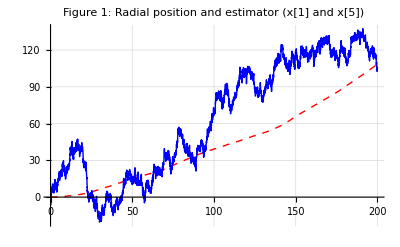

```mathematica
plots={{t,x[[1]]},{t,x[[5]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 1: Radial position and estimator (x[1] and x[5])",Joined->True,PlotStyle->{{Red,Dashed},Blue},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```

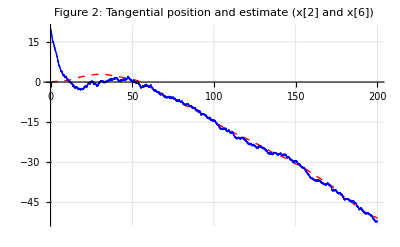

```mathematica
plots={{t,x[[2]]},{t,x[[6]]}};
plots=Map[Transpose,plots];
ListPlot[plots,PlotLabel->"Figure 2: Tangential position and estimate (x[2] and x[6])",Joined->True,PlotStyle->{{Red,Dashed},Blue},GridLines->Automatic,PerformanceGoal->"Speed",MaxPlotPoints->2000]
```